```mathematica
SetDirectory["/Users/Martin Zwierlein/Documents/Experiment/Feshbach/TieckeFeshbachModel"];
```

## General

### Initialization

```mathematica
Off[ClebschGordan::"phy"]
Off[General::"spell1"]
Off[General::"spell"]
<<"ErrorBarPlots`";<<"PlotLegends`"
```

### Constants

```mathematica
IILi6=1;
IILi7=3/2;
IINa23=3/2;         
IIK39=3/2;
IIK40=4;
IIK41=3/2;
IIRb85=5/2;
IIRb87=3/2;
IICs133=7/2;
```

```mathematica
SSLi6=1/2;
SSLi7=1/2;
SSNa23=1/2;
SSK39=1/2;
SSK40=1/2;
SSK41=1/2;
SSRb85=1/2;
SSRb87=1/2;
SSCs133=1/2;
```

```mathematica
AhfLi6=152.1368407*10^6;               (*arimondo*)
AhfLi7=401.7520433*10^6;               (*arimondo*)
AhfNa23=885.8130644*10^6;               (*arimondo*)
AhfK39=230.859860*10^6;               (*arimondo*)
AhfK40=-285.7308*10^6;               (*arimondo*)
AhfK41=127.0069352*10^6;               (*arimondo*)
AhfRb85=1011.910813*10^6;   (*arimondo*)
AhfRb87=3417.34130642*10^6;   (*arimondo*)
AhfCs133=2298.1579425*10^6;   (*arimondo*)
```

```mathematica
gS=2.0023193043622;                   (*NIST site*)
gILi6=-0.0004476540;               (*arimondo*)
gILi7=-0.0011822130;               (*arimondo*)
gINa23=-0.0008046108;               (*arimondo*)
gIK39=-0.00014193489;               (*arimondo*)
gIK40=+0.000176490;               (*arimondo*)
gIK41=-0.00007790600;               (*arimondo*)
gIRb85=-0.0002936400;          (*arimondo*)
gIRb87=-0.0009951414;          (*arimondo*)
gICs133=-0.00039885395;          (*arimondo*)
```

```mathematica
mLi6=6.0151223;                   (*NIST site*)
mLi7=7.0160040;                   (*NIST site*)
mNa23=22.98976967;                   (*NIST site*)
mK39=38.9637069;                   (*NIST site*)
mK40=39.96399867;                   (*NIST site*)
mK41=40.96182597;                   (*NIST site*)
mRb85=84.9117893;                   (*NIST site*)
mRb87=86.9091835;                   (*NIST site*)
mCs133=132.905447;                   (*NIST site*)
```

```mathematica
h=6.62606896*10^-34;                   (*NIST site*)
ℏ=h/(2π);
muB=9.27400915*10^-24;                   (*NIST site*)
a0SI=5.2917720859*10^-11;                   (*NIST site*)
a0=1;
hbar=1;
kB=1.3806504*10^-23;                   (*NIST site*)
me=9.10938215*10^-31;                   (*NIST site*)
u=1.660538782*10^-27;                   (*NIST site*)
```

```mathematica
C6Rb=4698 a0;                (* from Chris' thesis*)
C6LiK=2322 a0;            (*heternuclear C6 from Julienne/Tiesinga *)
(*C8LiK=192490;
C6LiNa=1459.4 a0;*)
Eh=4.35974394*10^-18;                   (*NIST site*)

(*THESE ARE THE PROPER (CHECKED) CONSTANTS!!! only if every constant is followed by a line which includes the reference*)
```

This variable is the stepsize (in Gauss) for which we calculate the molecular hyperfine states. For determining where the feshbach resonances are this value should be small (0.1G or so) however this makes the notebook slow and big, so for plotting use just use 3G or so.

```mathematica
deltaB=2.5;
minBPlot=0;
maxBPlot=1200;
highBLimit=1000;
```

## Choice of species

```mathematica
SS1=SSNa23;
SS2=SSK39;
II1=IINa23;
II2=IIK39;
Ahf1=AhfNa23;
Ahf2=AhfK39;
gI1=gINa23;
gI2=gIK39;
```

```mathematica
μ=(mNa23*mK39)/(mNa23+mK39)*u
```

2.40092×10^-26

```mathematica
maxTotalMF=SS1+SS2+II1+II2
```

4

## Free atom calculations

### Atom1

```mathematica
Ahf=Ahf1;
II=II1;
gI=gI1;
SS=SS1;
```

```mathematica
ISbasis=Flatten[Table[Table[{mI,mS},{mS,-SS,SS,1}],{mI,-II,II,1}],1]
```

{{-3/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{-1/2,1/2},{1/2,-1/2},{1/2,1/2},{3/2,-1/2},{3/2,1/2}}

```mathematica
FmFbasis=Flatten[Table[{FF,mF},{FF,II-SS,II+SS},{mF,-FF,FF,1}],1]
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
nStatesF=Length[FmFbasis]
nStatesI=Length[ISbasis]
```

8

8

```mathematica
ClebschMatrix=Table[ClebschGordan[{II,ISbasis[[iIS,1]]},{SS,ISbasis[[iIS,2]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}],{iFmF,1,nStatesF},{iIS,1,nStatesI}];
```

```mathematica
couplingMatrixElement=Table[1/2(FF(FF+1)-II(II+1)-SS(SS+1))/.{FF->FmFbasis[[i,1]]},{i,nStatesF}];
```

```mathematica
HyperfineH=Table[h*Ahf*(ClebschMatrix[[All,i]]*ClebschMatrix[[All,j]]).couplingMatrixElement,{i,nStatesI},{j,nStatesI}];
```

```mathematica
ZeemanH=Table[KroneckerDelta[i,j]*muB*B*10^-4*(gS*ISbasis[[i,2]]+gI*ISbasis[[i,1]]),{i,1,nStatesI},{j,1,nStatesI}];
```

```mathematica
TotalH=HyperfineH+ZeemanH;
```

```mathematica
TotalHAtom1=TotalH;
```

```mathematica
Energy=10^-6/h Eigenvalues[TotalH];
```

```mathematica
nStatesAtom1=Length[Energy];
```

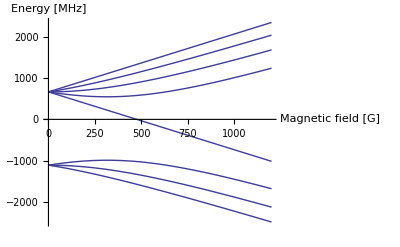

```mathematica
tmpPl=Table[0,{i,nStatesAtom1}];
For[i=1,i<=nStatesAtom1,
tmpPl[[i]]=Plot[Energy[[i]],{B,minBPlot,maxBPlot},AxesLabel->{"Magnetic field [G]","Energy [MHz]"},DisplayFunction->Identity];
i=i+1];
Show[tmpPl,DisplayFunction->$DisplayFunction,PlotRange->All]
```

```mathematica
Sort[Transpose[Eigensystem[TotalH/h/.B->maxBPlot]]]//MatrixForm
```

(-2.48211×10^9 | {0.,0.,0.,0.,0.,-0.172352,0.985035,0.}
-2.1226×10^9 | {0.,0.,0.,-0.239981,0.970778,0.,0.,0.}
-1.67759×10^9 | {0.,-0.273611,0.96184,0.,0.,0.,0.,0.}
-1.01511×10^9 | {1.,0.,0.,0.,0.,0.,0.,0.}
1.23739×10^9 | {0.,0.96184,0.273611,0.,0.,0.,0.,0.}
1.6797×10^9 | {0.,0.,0.,0.970778,0.239981,0.,0.,0.}
2.0365×10^9 | {0.,0.,0.,0.,0.,0.985035,0.172352,0.}
2.34383×10^9 | {0.,0.,0.,0.,0.,0.,0.,1.})

```mathematica
ISbasisAtom1=ISbasis
FmFbasisAtom1=FmFbasis
```

{{-3/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{-1/2,1/2},{1/2,-1/2},{1/2,1/2},{3/2,-1/2},{3/2,1/2}}

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
EnergyAtom1=Energy;
```

### Atom2

```mathematica
Ahf=Ahf2;
II=II2;
gI=gI2;
SS=SS2;
```

```mathematica
ISbasis=Flatten[Table[Table[{mI,mS},{mS,-SS,SS,1}],{mI,-II,II,1}],1]
```

{{-3/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{-1/2,1/2},{1/2,-1/2},{1/2,1/2},{3/2,-1/2},{3/2,1/2}}

```mathematica
FmFbasis=Flatten[Table[{FF,mF},{FF,II-SS,II+SS},{mF,-FF,FF,1}],1]
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
nStatesF=Length[FmFbasis]
nStatesI=Length[ISbasis]
```

8

8

```mathematica
ClebschMatrix=Table[ClebschGordan[{II,ISbasis[[iIS,1]]},{SS,ISbasis[[iIS,2]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}],{iFmF,1,nStatesF},{iIS,1,nStatesI}];
```

```mathematica
couplingMatrixElement=Table[1/2(FF(FF+1)-II(II+1)-SS(SS+1))/.{FF->FmFbasis[[i,1]]},{i,nStatesF}];
```

```mathematica
HyperfineH=Table[h*Ahf*(ClebschMatrix[[All,i]]*ClebschMatrix[[All,j]]).couplingMatrixElement,{i,nStatesI},{j,nStatesI}];
```

```mathematica
ZeemanH=Table[KroneckerDelta[i,j]*muB*B*10^-4*(gS*ISbasis[[i,2]]+gI*ISbasis[[i,1]]),{i,1,nStatesI},{j,1,nStatesI}];
```

```mathematica
TotalH=HyperfineH+ZeemanH;
```

```mathematica
TotalHAtom2=TotalH;
```

```mathematica
Energy=10^-6/h Eigenvalues[TotalH];
```

```mathematica
nStatesAtom2=Length[Energy];
```

```mathematica
Energy
```

{1.50919×10^27 (1.14727×10^-25-9.28279×10^-28 B),1.50919×10^27 (1.14727×10^-25+9.28279×10^-28 B),7.54595×10^26 (-7.64847×10^-26-√(9.35985×10^-50+3.44876×10^-54 B^2)),7.54595×10^26 (-7.64847×10^-26+√(9.35985×10^-50+3.44876×10^-54 B^2)),7.54595×10^26 (-7.64847×10^-26+2.63261×10^-31 B-√(9.35985×10^-50-5.68154×10^-52 B+3.44876×10^-54 B^2)),7.54595×10^26 (-7.64847×10^-26+2.63261×10^-31 B+√(9.35985×10^-50-5.68154×10^-52 B+3.44876×10^-54 B^2)),7.54595×10^26 (-7.64847×10^-26-2.63261×10^-31 B-√(9.35985×10^-50+5.68154×10^-52 B+3.44876×10^-54 B^2)),7.54595×10^26 (-7.64847×10^-26-2.63261×10^-31 B+√(9.35985×10^-50+5.68154×10^-52 B+3.44876×10^-54 B^2))}

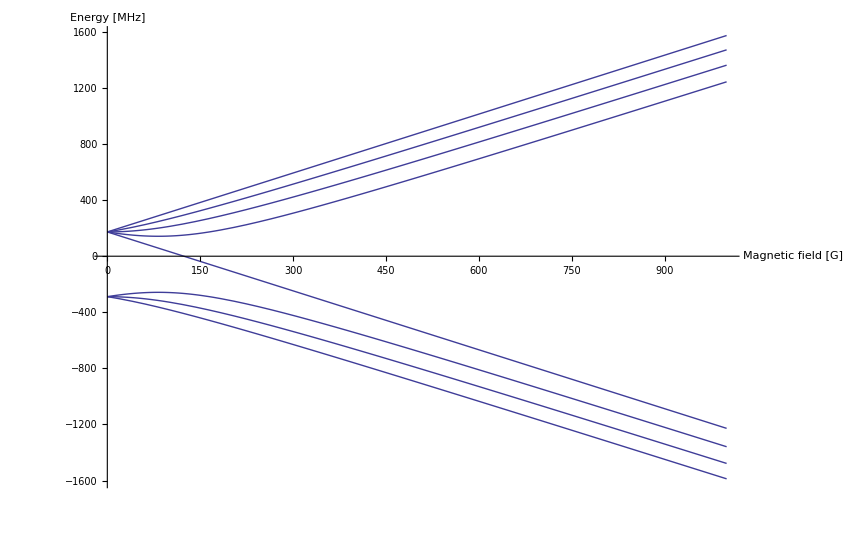

```mathematica
tmpPl=Table[0,{i,nStatesAtom2}];
For[i=1,i<=nStatesAtom2,
tmpPl[[i]]=Plot[Energy[[i]],{B,0,1000},AxesLabel->{"Magnetic field [G]","Energy [MHz]"},DisplayFunction->Identity];
i=i+1];
Show[tmpPl,DisplayFunction->$DisplayFunction,PlotRange->All]
```

```mathematica
Sort[Transpose[Eigensystem[TotalH/h/.B->maxBPlot]]]//MatrixForm
```

(-1.86609×10^9 | {0.,0.,0.,0.,0.,-0.0553714,0.998466,0.}
-1.7551×10^9 | {0.,0.,0.,-0.0681629,0.997674,0.,0.,0.}
-1.63637×10^9 | {0.,-0.0634412,0.997986,0.,0.,0.,0.,0.}
-1.50799×10^9 | {1.,0.,0.,0.,0.,0.,0.,0.}
1.52142×10^9 | {0.,0.997986,0.0634412,0.,0.,0.,0.,0.}
1.63967×10^9 | {0.,0.,0.,0.997674,0.0681629,0.,0.,0.}
1.75018×10^9 | {0.,0.,0.,0.,0.,0.998466,0.0553714,0.}
1.85428×10^9 | {0.,0.,0.,0.,0.,0.,0.,1.})

```mathematica
ISbasisAtom2=ISbasis
FmFbasisAtom2=FmFbasis
```

{{-3/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{-1/2,1/2},{1/2,-1/2},{1/2,1/2},{3/2,-1/2},{3/2,1/2}}

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
EnergyAtom2=Energy;
```

### sorted bases

#### Atom 1

```mathematica
highFieldEn=EnergyAtom1/.B->highBLimit
```

{-735.199,2063.92,-1879.69,1436.78,-1448.33,1007.68,-2220.45,1775.29}

```mathematica
sortedEns=Sort[highFieldEn]
```

{-2220.45,-1879.69,-1448.33,-735.199,1007.68,1436.78,1775.29,2063.92}

```mathematica
sEnergyAtom1={};
For[i=1,i≤nStatesAtom1,
pos=Flatten[Position[highFieldEn,sortedEns[[i]]]][[1]];
AppendTo[sEnergyAtom1,EnergyAtom1[[pos]]];
i++];
```

```mathematica
sFmFAtom1={{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}
```

{{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
MatrixForm[sEnergyAtom1/.B->highBLimit]
```

(-2220.45
-1879.69
-1448.33
-735.199
1007.68
1436.78
1775.29
2063.92)

#### Atom 2

```mathematica
highFieldEn=EnergyAtom2/.B->highBLimit
```

{-1227.8,1574.09,-1477.95,1362.52,-1358.88,1243.85,-1587.81,1471.98}

```mathematica
sortedEns=Sort[highFieldEn]
```

{-1587.81,-1477.95,-1358.88,-1227.8,1243.85,1362.52,1471.98,1574.09}

```mathematica
sEnergyAtom2={};
For[i=1,i≤nStatesAtom2,
pos=Flatten[Position[highFieldEn,sortedEns[[i]]]][[1]];
AppendTo[sEnergyAtom2,EnergyAtom2[[pos]]];
i++];
```

```mathematica
sFmFAtom2={{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2},{7/2,7/2},{7/2,5/2},{7/2,3/2},{7/2,1/2},{7/2,-1/2},{7/2,-3/2},{7/2,-5/2},{7/2,-7/2}}
```

{{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2},{7/2,7/2},{7/2,5/2},{7/2,3/2},{7/2,1/2},{7/2,-1/2},{7/2,-3/2},{7/2,-5/2},{7/2,-7/2}}

```mathematica
stateList={};
For[iAtom1=1,iAtom1≤nStatesAtom1,
For[iAtom2=1,iAtom2≤nStatesAtom2,
totalMF=sFmFAtom1[[iAtom1,2]]+sFmFAtom2[[iAtom2,2]];
AppendTo[stateList,{totalMF,iAtom1,iAtom2}];
iAtom2++];iAtom1++]
```

```mathematica
toPlot=Flatten[{Table[stateList[[i]],{i,1,10}],{stateList[[1*18+1]],stateList[[2*18+1]]}},1]
```

{{-7/2,1,1},{-5/2,1,2},{-3/2,1,3},{-1/2,1,4},{1/2,1,5},{3/2,1,6},{5/2,1,7},{7/2,1,8},{-9/2,2,1},{-7/2,2,2},{-7/2,3,3},{-3/2,5,5}}

## ABM Hamiltonian construction

```mathematica
bindingEnergies={{ϵ0,ϵ1},{ϵ20,ϵ21}};
```

```mathematica
overlap=({{1, η0, 0, η2}, {η0, 1, η1, 0}, {0, η1, 1, η3}, {η2, 0, η3, 1}});
```

```mathematica
nVibrLevels=1;
```

```mathematica
overlapMatrix=Table[overlap[[ss+2*(nn-1)]][[ssp+2*(nnp-1)]],{ss,1,2},{nn,1,nVibrLevels},{ssp,1,2},{nnp,1,nVibrLevels}];
```

```mathematica
MFValue=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
TotalHMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
HintMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
PSingletMF = Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
PTripletMF = Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
ISbasisMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
FmFbasisMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
ClebschMatMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
```

```mathematica
For[iMF=1,iMF≤2*maxTotalMF+1,
totalMF=-maxTotalMF+(iMF-1);
ISbasis={};
mS1=-SS1;
mS2=SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1/(√2),mS1,mS2,-1/(√2),-mS1,-mS2,0,0,1}]];
mI2++];
mI1++];

mS1=SS1;
mS2=SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1,mS1,mS2,0,0,0,1,1,1}]];
mI2++];
mI1++];

mS1=-SS1;
mS2=SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1/(√2),mS1,mS2,1/(√2),-mS1,-mS2,1,0,1}]];
mI2++];
mI1++];

mS1=-SS1;
mS2=-SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1,mS1,mS2,0,0,0,1,-1,1}]];
mI2++];
mI1++];
ISbasis//MatrixForm;

FmFbasis={};
For[kk=1,kk≤Length[stateList],
If[sFmFAtom1[[stateList[[kk,2]],2]]+sFmFAtom2[[stateList[[kk,3]],2]]==totalMF,AppendTo[FmFbasis,Flatten[{sFmFAtom1[[stateList[[kk,2]]]],sFmFAtom2[[stateList[[kk,3]]]]}]]];
kk++];
tmpBasis=FmFbasis;
For[iVbr=1,iVbr<nVibrLevels,
FmFbasis=Flatten[{FmFbasis,tmpBasis},1];
iVbr++];

Length[FmFbasis]

tmpBasis=ISbasis;
For[iVbr=1,iVbr<nVibrLevels,
tmpBasis2=tmpBasis;
tmpBasis2[[All,11]]=iVbr+1;
ISbasis=Flatten[{ISbasis,tmpBasis2},1];
iVbr++];

nStatesF=Length[FmFbasis];
nStatesI=Length[ISbasis];
ClebschMatrixT=1/(√nVibrLevels)Table[ISbasis[[iIS,3]]*
(ClebschGordan[{II1,ISbasis[[iIS,1]]},{SS1,ISbasis[[iIS,4]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}])*
(ClebschGordan[{II2,ISbasis[[iIS,2]]},{SS2,ISbasis[[iIS,5]]},{FmFbasis[[iFmF,3]],FmFbasis[[iFmF,4]]}])+
ISbasis[[iIS,6]]*
(ClebschGordan[{II1,ISbasis[[iIS,1]]},{SS1,ISbasis[[iIS,7]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}])*
(ClebschGordan[{II2,ISbasis[[iIS,2]]},{SS2,ISbasis[[iIS,8]]},{FmFbasis[[iFmF,3]],FmFbasis[[iFmF,4]]}]),
{iFmF,1,nStatesF},{iIS,1,nStatesI}];

couplingMatrixElementT=Table[(Ahf1 1/2(FF1(FF1+1)-II1(II1+1)-SS1(SS1+1))+Ahf2 1/2(FF2(FF2+1)-II2(II2+1)-SS2(SS2+1)))/.{FF1->FmFbasis[[i,1]],FF2->FmFbasis[[i,3]]},{i,nStatesF}];
HyperfineH=Table[(h*(ClebschMatrixT[[All,i]]*ClebschMatrixT[[All,j]]).couplingMatrixElementT),{i,nStatesI},{j,nStatesI}];

ZeemanH=Table[KroneckerDelta[i,j]*muB*B*10^-4*
(gS*(ISbasis[[i,10]])+
gI1*ISbasis[[i,1]]+
gI2*ISbasis[[i,2]]),
{i,1,nStatesI},{j,1,nStatesI}];

Hexch=Table[KroneckerDelta[i,j]*h*10^6*bindingEnergies[[ISbasis[[i,11]],(ISbasis[[i,9]]+1)]],{i,1,nStatesI},{j,1,nStatesI}];

OverlapH=Table[overlapMatrix[[ISbasis[[i,9]]+1,ISbasis[[i,11]],ISbasis[[j,9]]+1,ISbasis[[j,11]]]],{i,1,nStatesI},{j,1,nStatesI}];

PTriplet = Table[KroneckerDelta[i,j]*ISbasis[[i,9]],{i,1,nStatesI},{j,1,nStatesI}];
PSinglet = Table[KroneckerDelta[i,j]*(1-ISbasis[[i,9]]),{i,1,nStatesI},{j,1,nStatesI}];

MFValue[[iMF]]=totalMF;
TotalHMF[[iMF]]=OverlapH*(HyperfineH+ZeemanH+Hexch);
HintMF[[iMF]]=(HyperfineH+ZeemanH);
ISbasisMF[[iMF]]=ISbasis;
FmFbasisMF[[iMF]]=FmFbasis;
ClebschMatMF[[iMF]]=ClebschMatrixT;
PTripletMF[[iMF]] = PTriplet;
PSingletMF[[iMF]] = PSinglet;
iMF++;]
```

```mathematica
iState =4;
sFmFAtom1[[stateList[[iState,2]]]]
sFmFAtom2[[stateList[[iState,3]]]]
totalMF = stateList⟦iState,1⟧;
hamiltonPos=Flatten[Position[MFValue,totalMF],1]⟦1⟧;
Hint=10^-9/h HintMF⟦hamiltonPos⟧;
PSinglet = PSingletMF[[hamiltonPos]];
PTriplet = PTripletMF[[hamiltonPos]];
m=Hint;
v=Eigenvectors[m]/.{B->138};
aT = -805-150
aS = 69
aT*Normalize[v[[1]]].PTriplet.Normalize[v[[1]]]+aS*Normalize[v[[1]]].PSinglet.Normalize[v[[1]]]/.{B->138}

Plot[ aT*Normalize[v[[1]]].PTriplet.Normalize[v[[1]]]+aS*Normalize[v[[1]]].PSinglet.Normalize[v[[1]]],{B,0,1000}]
```

{1,1}

{9/2,-3/2}

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

-955

69

69 (1. {{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧)/Abs[{{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧].{{{0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0}}}⟦{}⟦1⟧⟧.(1. {{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧)/Abs[{{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧]-955 (1. {{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧)/Abs[{{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧].{{{1}},{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{1}}}⟦{}⟦1⟧⟧.(1. {{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧)/Abs[{{{-2.56078×10^-25}},{{1.8171×10^-28,0.,0.,0.},{0.,1.8171×10^-28,0.,0.},{0.,0.,-2.56096×10^-25,0.},{0.,0.,0.,-2.56181×10^-25}},{{1.63545×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,7.87351×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.56441×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.63545×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,7.87351×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.56114×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.56199×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56284×10^-25}},{{1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56423×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56338×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.4538×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.05701×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.56132×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56217×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56302×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56387×10^-25}},{{1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.24051×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.27215×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56405×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.5632×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56235×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.27215×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.24051×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.24051×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.27215×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56235×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.5632×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56405×10^-25}},{{2.42401×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.05701×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.4538×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.56387×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.56302×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.56217×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.56132×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.42401×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.05701×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.4538×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56338×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.56423×10^-25}},{{-7.87351×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.63545×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.56284×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.56199×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.56114×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-7.87351×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.63545×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.56441×10^-25}},{{-1.8171×10^-28,0.,0.,0.},{0.,2.56181×10^-25,0.,0.},{0.,0.,2.56096×10^-25,0.},{0.,0.,0.,-1.8171×10^-28}},{{2.56078×10^-25}}}⟦{}⟦1⟧⟧]

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

-Graphics-

```mathematica
aT*Eigenvectors[Hint][[1]].PTriplet.Eigenvectors[Hint][[1]]+aS*Eigenvectors[Hint][[1]].PSinglet.Eigenvectors[Hint][[1]]/.B->150
```

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

69 (1.50919×10^24 {{{-2.78345×10^-25}},{{1.97511×10^-28,0.,0.,0.},{0.,1.97511×10^-28,0.,0.},{0.,0.,-2.78365×10^-25,0.},{0.,0.,0.,-2.78457×10^-25}},{{1.77767×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,8.55816×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.7874×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.77767×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,8.55816×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.78385×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.78477×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.78569×10^-25}},{{1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78721×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78628×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.58022×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.58371×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.78405×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78497×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78589×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78681×10^-25}},{{1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78701×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78609×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78517×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.38277×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.60925×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.60925×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.38277×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78517×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78609×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78701×10^-25}},{{2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78681×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78589×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78497×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78405×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.58371×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.58022×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78628×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78721×10^-25}},{{-8.55816×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.77767×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.78569×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.78477×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.78385×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-8.55816×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.77767×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.7874×10^-25}},{{-1.97511×10^-28,0.,0.,0.},{0.,2.78457×10^-25,0.,0.},{0.,0.,2.78365×10^-25,0.},{0.,0.,0.,-1.97511×10^-28}},{{2.78345×10^-25}}}⟦{}⟦1⟧⟧).{{{0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0}}}⟦{}⟦1⟧⟧.(1.50919×10^24 {{{-2.78345×10^-25}},{{1.97511×10^-28,0.,0.,0.},{0.,1.97511×10^-28,0.,0.},{0.,0.,-2.78365×10^-25,0.},{0.,0.,0.,-2.78457×10^-25}},{{1.77767×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,8.55816×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.7874×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.77767×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,8.55816×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.78385×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.78477×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.78569×10^-25}},{{1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78721×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78628×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.58022×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.58371×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.78405×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78497×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78589×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78681×10^-25}},{{1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78701×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78609×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78517×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.38277×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.60925×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.60925×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.38277×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78517×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78609×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78701×10^-25}},{{2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78681×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78589×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78497×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78405×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.58371×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.58022×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78628×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78721×10^-25}},{{-8.55816×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.77767×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.78569×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.78477×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.78385×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-8.55816×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.77767×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.7874×10^-25}},{{-1.97511×10^-28,0.,0.,0.},{0.,2.78457×10^-25,0.,0.},{0.,0.,2.78365×10^-25,0.},{0.,0.,0.,-1.97511×10^-28}},{{2.78345×10^-25}}}⟦{}⟦1⟧⟧)-955 (1.50919×10^24 {{{-2.78345×10^-25}},{{1.97511×10^-28,0.,0.,0.},{0.,1.97511×10^-28,0.,0.},{0.,0.,-2.78365×10^-25,0.},{0.,0.,0.,-2.78457×10^-25}},{{1.77767×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,8.55816×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.7874×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.77767×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,8.55816×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.78385×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.78477×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.78569×10^-25}},{{1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78721×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78628×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.58022×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.58371×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.78405×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78497×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78589×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78681×10^-25}},{{1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78701×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78609×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78517×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.38277×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.60925×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.60925×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.38277×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78517×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78609×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78701×10^-25}},{{2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78681×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78589×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78497×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78405×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.58371×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.58022×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78628×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78721×10^-25}},{{-8.55816×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.77767×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.78569×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.78477×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.78385×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-8.55816×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.77767×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.7874×10^-25}},{{-1.97511×10^-28,0.,0.,0.},{0.,2.78457×10^-25,0.,0.},{0.,0.,2.78365×10^-25,0.},{0.,0.,0.,-1.97511×10^-28}},{{2.78345×10^-25}}}⟦{}⟦1⟧⟧).{{{1}},{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{1}}}⟦{}⟦1⟧⟧.(1.50919×10^24 {{{-2.78345×10^-25}},{{1.97511×10^-28,0.,0.,0.},{0.,1.97511×10^-28,0.,0.},{0.,0.,-2.78365×10^-25,0.},{0.,0.,0.,-2.78457×10^-25}},{{1.77767×10^-28,0.,0.,0.,0.,0.,0.,0.},{0.,8.55816×10^-29,0.,0.,0.,0.,0.,0.},{0.,0.,2.7874×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,1.77767×10^-28,0.,0.,0.,0.},{0.,0.,0.,0.,8.55816×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,-2.78385×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,-2.78477×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,-2.78569×10^-25}},{{1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78721×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78628×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.58022×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,6.58371×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-2.78405×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78497×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78589×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78681×10^-25}},{{1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-4.60925×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.38277×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78701×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78609×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78517×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.38277×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.60925×10^-29,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.60925×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.38277×10^-28,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78517×10^-25,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78609×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78701×10^-25}},{{2.63479×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-6.58371×10^-29,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-1.58022×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.78681×10^-25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.78589×10^-25,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,2.78497×10^-25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.78405×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.63479×10^-29,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-6.58371×10^-29,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.58022×10^-28,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78628×10^-25,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.78721×10^-25}},{{-8.55816×10^-29,0.,0.,0.,0.,0.,0.,0.},{0.,-1.77767×10^-28,0.,0.,0.,0.,0.,0.},{0.,0.,2.78569×10^-25,0.,0.,0.,0.,0.},{0.,0.,0.,2.78477×10^-25,0.,0.,0.,0.},{0.,0.,0.,0.,2.78385×10^-25,0.,0.,0.},{0.,0.,0.,0.,0.,-8.55816×10^-29,0.,0.},{0.,0.,0.,0.,0.,0.,-1.77767×10^-28,0.},{0.,0.,0.,0.,0.,0.,0.,-2.7874×10^-25}},{{-1.97511×10^-28,0.,0.,0.},{0.,2.78457×10^-25,0.,0.},{0.,0.,2.78365×10^-25,0.},{0.,0.,0.,-1.97511×10^-28}},{{2.78345×10^-25}}}⟦{}⟦1⟧⟧)

```mathematica
Evaltab = Table[Flatten[{Bp,Sort[Eigenvalues[Hint/.B->Bp]]}],{Bp,minBPlot,maxBPlot,(maxBPlot-minBPlot)/200}];
```

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

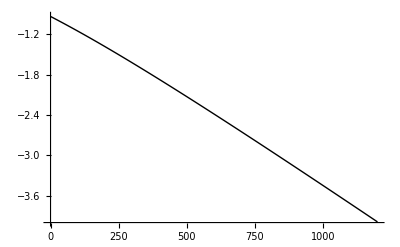

```mathematica
Show[Plot[(sEnergyAtom1⟦stateList⟦iState,2⟧⟧+sEnergyAtom2⟦stateList⟦iState,3⟧⟧)/10^3/.{B->Bp},{Bp,minBPlot,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[Evaltab[[All,{1,1+#}]]&/@Range[Length[Evaltab[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],PlotRange->All]
```

```mathematica
For[iState=1,iState≤10,
test =sFmFAtom2[[stateList[[iState,3]]]];
iState++];
test
```

{9/2,-7/2}

## s-p-d wave parameterization and overlap param.

```mathematica
allEta=Import["allEta.csv"];
```

Import::nffil: File not found during Import.

```mathematica
SPparam=Import["SPparam.csv"];
SDparam=Import["SDparam.csv"];
```

Import::nffil: File not found during Import.

```mathematica
ηInterp=Interpolation[allEta];
```

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
SPInterp=Interpolation[SPparam];
SDInterp=Interpolation[SDparam];
```

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
SPparam2=Import["SPparam2.csv"];
SDparam2=Import["SDparam2.csv"];
SPInterp2=Interpolation[SPparam2];
SDInterp2=Interpolation[SDparam2];
```

Import::nffil: File not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

## Calculate spectra

```mathematica
getBS2[oE0_,oE1_,oE02_,oE12_,oη0_,oη1_,oη2_,oη3_,ΔMF_]:=Module[{},
iState=toPlot⟦1⟧;
totalMF=stateList⟦iState,1⟧+ΔMF;
hamiltonPos=Flatten[Position[MFValue,totalMF],1]⟦1⟧;
TotalH=TotalHMF⟦hamiltonPos⟧/.{ϵ0->oE0,ϵ1->oE1,ϵ20->oE02,ϵ21->oE12,η0->oη0,η1->oη1,η2->oη2,η3->oη3};
ISbasis=ISbasisMF[[hamiltonPos]];
openChanFn[B_]=(sEnergyAtom1⟦stateList⟦iState,2⟧⟧+sEnergyAtom2⟦stateList⟦iState,3⟧⟧)/10^3;Table[Flatten[{Bp,Sort[Eigenvalues[-0*openChanFn[Bp]*IdentityMatrix[Length[TotalH]]+10^-9/h TotalH/.B->Bp]]}],{Bp,minBPlot,maxBPlot,(maxBPlot-minBPlot)/200}]
];
getHyperfine[oE0_,oE1_,oE02_,oE12_,oη0_,oη1_,oη2_,oη3_,ΔMF_]:=Module[{},
iState=toPlot⟦1⟧;
totalMF=stateList⟦iState,1⟧+ΔMF;
hamiltonPos=Flatten[Position[MFValue,totalMF],1]⟦1⟧;
Hint=HintMF⟦hamiltonPos⟧/.{ϵ0->oE0,ϵ1->oE1,ϵ20->oE02,ϵ21->oE12,η0->oη0,η1->oη1,η2->oη2,η3->oη3};
ISbasis=ISbasisMF[[hamiltonPos]];
openChanFn[B_]=(sEnergyAtom1⟦stateList⟦iState,2⟧⟧+sEnergyAtom2⟦stateList⟦iState,3⟧⟧)/10^3;Table[Flatten[{Bp,Sort[Eigenvalues[10^-9/h Hint/.B->Bp]]}],{Bp,minBPlot,maxBPlot,(maxBPlot-minBPlot)/200}]
];
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

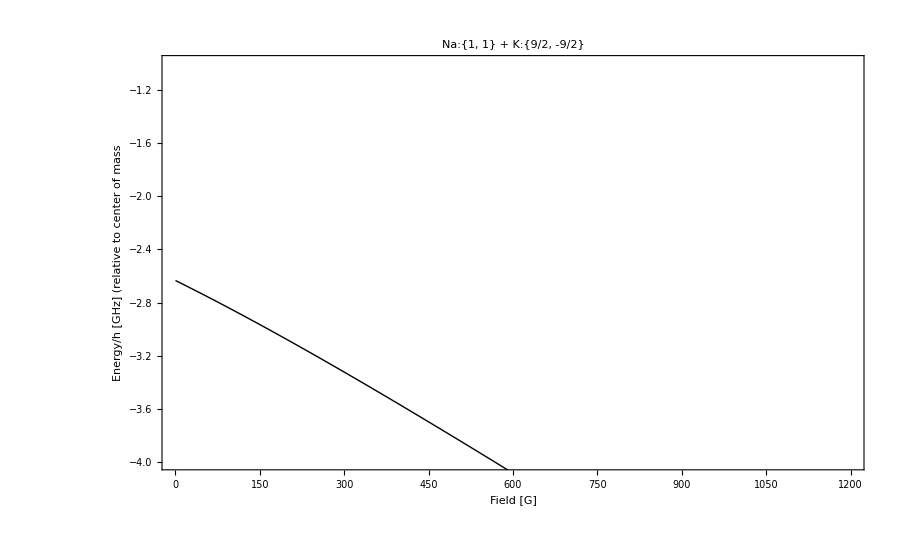

```mathematica
toPlot={1};
qqhyperfine =getHyperfine[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
Show[Plot[-1.7+(sEnergyAtom1⟦stateList⟦4,2⟧⟧+sEnergyAtom2⟦stateList⟦4,3⟧⟧)/10^3/.{B->Bp},{Bp,minBPlot,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqhyperfine[[All,{1,1+#}]]&/@{1},PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
PlotRange->{-4,-1},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->900,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

```mathematica
MeasRes={{1,5.72},{1,6.01},{1,20.45},{1,20.55},{1,78.3},{1,88.2},{2,6.77},{2,7.01},{2,23.19},{2,23.29},{2,81.6},{2,89.9},{2,108.6},{3,8.91},{3,9.33},{3,29.2},{3,29.52},{3,97.5},{3,106.9},{3,148.3},{4,12.51},{4,12.68},{4,39.39},{4,39.86},{4,116},{4,129},{4,180},{5,0},{6,0},{7,0},{8,0},{9,0},{10,274.9}};
```

E0S/E1S are the singlet/triplet energies of one vibrational manifold
E0S2/E1S2 are the singlet/triplet energies of another vibrational manifold

η0S is the overlap between E0S and E1S
η1S is the overlap between E1S and E0S2
η2S is the overlap between E0S and E1S2
η3S is the overlap between E0S2 and E1S2

overlap=(1 | η0S | 0 | η2S
η0S | 1 | η1S | 0
0 | η1S | 1 | η3S
η2S | 0 | η3S | 1);

```mathematica
E0S=-148.7;
E1S=-1623.53;

E0S2=40000.0;
E1S2=0.5;
E0P=-SPInterp[-E0S];
E1P=-SPInterp[-E1S];
η0P=ηInterp[-E0P,-E1P];

E0D=-SDInterp[-E0S];
E1D=-SDInterp[-E1S];
η0D=ηInterp[-E0D,-E1D];


η0S=ηInterp[-E0S,-E1S];
(*η1S=ηInterp[-E1S,-E0S2];
η2S=ηInterp[-E1S2,-E0S];
η3S=ηInterp[-E0S2,-E1S2];*)
η1S=0.0;
η2S=0.93;
η3S=0.0;
minBPlot=0;
maxBPlot=400;
```

```mathematica
E0S=-148.7;
E1S=-1655;

E0S2=40000.0;
E1S2=.5;
E0P=-SPInterp[-E0S];
E1P=-SPInterp[-E1S]+20;
η0P=ηInterp[-E0P,-E1P];
η0P=.6;
E0D=-SDInterp[-E0S];
E1D=-SDInterp[-E1S]+55;
η0D=ηInterp[-E0D,-E1D];


η0S=ηInterp[-E0S,-E1S];
(*η1S=ηInterp[-E1S,-E0S2];
η2S=ηInterp[-E1S2,-E0S];
η3S=ηInterp[-E0S2,-E1S2];*)
η1S=0.0;
η2S=0.920;
η2S=0;

η3S=0.0;
minBPlot=100;
maxBPlot=200;
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 5 of {« 1 »} does not exist.

1.33598+«1»

94.6907

Part::partw: Part 5 of {100, 0, 3.01838×10^24\ {{{-1.28218×10^-24}}, {{-9.8398×10^-26, 0., 0., 0.}, {0., -1.09648×10^-24, 0., 0.}, {0., 0., -1.28219×10^-24, 0.}, {0., 0., 0., -1.28225×10^-24}}, « 5 », {{-9.86613×10^-26, 0., 0., 0.}, {0., -9.10976×10^-25, 0., 0.}, {0., 0., -9.11038×10^-25, 0.}, {0., 0., 0., -1.09675×10^-24}}, {{-9.11051×10^-25}}} ⟦ {} ⟦ 1 ⟧ ⟧} does not exist.

MapThread::mptd: Object {{100, 0, 3.01838×10^24\ {{{« 1 »}}, {{« 4 »}, {« 4 »}, {« 4 »}, {« 4 »}}, {{« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}}, {{« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}}, {{« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}, {« 14 »}}, {{« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}, {« 12 »}}, {{« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}, {« 8 »}}, {{« 4 »}, {« 4 »}, {« 4 »}, {« 4 »}}, {{« 1 »}}} ⟦ {} ⟦ 1 ⟧ ⟧}, « 49 », « 151 »} ⟦ All, 5 ⟧ at position {2, 2} in MapThread[{#1, -k^2 + openChanFn[#1]}/. Solve[Slot[« 1 »] + Times[« 2 »] + Times[« 2 »] == -Power[« 2 »], k] ⟦ 3 ⟧ &, {{100, 201/2, 101, 203/2, 102, 205/2, 103, 207/2, 104, 209/2, 105, 211/2, 106, 213/2, 107, 215/2, 108, 217/2, 109, 219/2, 110, 221/2, 111, 223/2, 112, 225/2, 113, 227/2, 114, 229/2, 115, 231/2, 116, 233/2, 117, 235/2, 118, 237/2, 119, 239/2, 120, 241/2, 121, 243/2, 122, 245/2, 123, 247/2, 124, 249/2, « 151 »}, {{100, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {201/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {101, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {203/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, « 43 », {247/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {124, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {249/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, « 151 »} ⟦ All, 5 ⟧}]
 has only 0 of required 1 dimensions.

ListPlot::lpn: MapThread[{#1, -k^2 + openChanFn[#1]}/. Solve[Slot[« 1 »] + Times[« 2 »] + Times[« 2 »] == -Power[« 2 »], k] ⟦ 3 ⟧ &, {{100, 201/2, 101, 203/2, 102, 205/2, 103, 207/2, 104, 209/2, 105, 211/2, 106, 213/2, 107, 215/2, 108, 217/2, 109, 219/2, 110, 221/2, 111, 223/2, 112, 225/2, 113, 227/2, 114, 229/2, 115, 231/2, 116, 233/2, 117, 235/2, 118, 237/2, 119, 239/2, 120, 241/2, 121, 243/2, 122, 245/2, 123, 247/2, 124, 249/2, « 151 »}, {{100, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {201/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {101, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {203/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, « 43 », {247/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {124, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {249/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, « 151 »} ⟦ All, 5 ⟧}]
 is not a list of numbers or pairs of numbers.

ListPlot[MapThread[{#1,-k^2+openChanFn[#1]}/.Solve[#2-openChanFn[#1]-Avs/(2 (kvs (k+kvs)))==-k^2,k]⟦3⟧&,{{100,201/2,101,203/2,102,205/2,103,207/2,104,209/2,105,211/2,106,213/2,107,215/2,108,217/2,109,219/2,110,221/2,111,223/2,112,225/2,113,227/2,114,229/2,115,231/2,116,233/2,117,235/2,118,237/2,119,239/2,120,241/2,121,243/2,122,245/2,123,247/2,124,249/2,125,251/2,126,253/2,127,255/2,128,257/2,129,259/2,130,261/2,131,263/2,«74»,169,339/2,170,341/2,171,343/2,172,345/2,173,347/2,174,349/2,175,351/2,176,353/2,177,355/2,178,357/2,179,359/2,180,361/2,181,363/2,182,365/2,183,367/2,184,369/2,185,371/2,186,373/2,187,375/2,188,377/2,189,379/2,190,381/2,191,383/2,192,385/2,193,387/2,194,389/2,195,391/2,196,393/2,197,395/2,198,397/2,199,399/2,200},«1»}],«2»,«9»→«1»]

Part::partw: Part {1, 5} of {100, 0, 3.01838×10^24\ {{{-1.28218×10^-24}}, {{-9.8398×10^-26, 0., 0., 0.}, {0., -1.09648×10^-24, 0., 0.}, {0., 0., -1.28219×10^-24, 0.}, {0., 0., 0., -1.28225×10^-24}}, « 5 », {{-9.86613×10^-26, 0., 0., 0.}, {0., -9.10976×10^-25, 0., 0.}, {0., 0., -9.11038×10^-25, 0.}, {0., 0., 0., -1.09675×10^-24}}, {{-9.11051×10^-25}}} ⟦ {} ⟦ 1 ⟧ ⟧} does not exist.

Part::partw: Part {1, 6} of {100, 0, 3.01838×10^24\ {{{-1.28218×10^-24}}, {{-9.8398×10^-26, 0., 0., 0.}, {0., -1.09648×10^-24, 0., 0.}, {0., 0., -1.28219×10^-24, 0.}, {0., 0., 0., -1.28225×10^-24}}, « 5 », {{-9.86613×10^-26, 0., 0., 0.}, {0., -9.10976×10^-25, 0., 0.}, {0., 0., -9.11038×10^-25, 0.}, {0., 0., 0., -1.09675×10^-24}}, {{-9.11051×10^-25}}} ⟦ {} ⟦ 1 ⟧ ⟧} does not exist.

Part::partw: Part {1, 7} of {100, 0, 3.01838×10^24\ {{{-1.28218×10^-24}}, {{-9.8398×10^-26, 0., 0., 0.}, {0., -1.09648×10^-24, 0., 0.}, {0., 0., -1.28219×10^-24, 0.}, {0., 0., 0., -1.28225×10^-24}}, « 5 », {{-9.86613×10^-26, 0., 0., 0.}, {0., -9.10976×10^-25, 0., 0.}, {0., 0., -9.11038×10^-25, 0.}, {0., 0., 0., -1.09675×10^-24}}, {{-9.11051×10^-25}}} ⟦ {} ⟦ 1 ⟧ ⟧} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPlot::lpn: MapThread[{#1, -k^2 + openChanFn[#1]}/. Solve[Slot[« 1 »] + Times[« 2 »] + Times[« 2 »] == -Power[« 2 »], k] ⟦ 3 ⟧ &, {{100, 201/2, 101, 203/2, 102, 205/2, 103, 207/2, 104, 209/2, 105, 211/2, 106, 213/2, 107, 215/2, 108, 217/2, 109, 219/2, 110, 221/2, 111, 223/2, 112, 225/2, 113, 227/2, 114, 229/2, 115, 231/2, 116, 233/2, 117, 235/2, 118, 237/2, 119, 239/2, 120, 241/2, 121, 243/2, 122, 245/2, 123, 247/2, 124, 249/2, « 151 »}, {{100, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {201/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {101, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {203/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, « 43 », {247/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {124, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, {249/2, 0, 3.01838×10^24\ {« 9 »} ⟦ Part[« 2 »] ⟧}, « 151 »} ⟦ All, 5 ⟧}]
 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], GrayLevel[0], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[27]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[100.`, -1.3800000000000001`]], Rule[PlotRange, List[List[100, 200], List[-1.3830556372153728`, -1.1520976894420607`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], GraphicsBox[List[], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]], ListPlot[« 1 »], GraphicsBox[List[List[List[], List[Hue[0.67`, 0.6`, 0.6`], PointSize[0.015`], PointBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]]]]], List[]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[116.`, -1.335`]], Rule[PlotRange, List[List[116.`, 180.`], List[-1.3359823551142591`, -1.1882663742415152`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], PlotRange → {-2, -1.8`}, PlotLabel → .

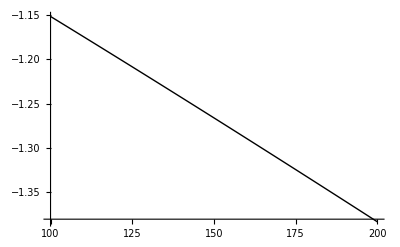
Show[-Graphics-,-Graphics-,«7»,FrameLabel→{Field [G],Energy/h [GHz] (relative to center of mass},FrameStyle→18]

```mathematica
toPlot={4};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
Avs = .0000946907;
evs =.0005;
kvs = √evs;
qqS[[161,5]]-openChanFn[180]
Avs*10^6
MolEnergyshifted =MapThread[{#1,-k^2+openChanFn[#1]}/.Solve[#2-openChanFn[#1]-(Avs/2)/(kvs(k+kvs))==-k^2,k][[3]]&,{qqS[[All,1]],qqS[[All,5]]}];
ListPlot[MolEnergyshifted,PlotRange->All,Joined->5True,PlotStyle->Darker[Red]]
Show[Plot[openChanFn[B],{B,minBPlot,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@{4,5,6},PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[MolEnergyshifted,PlotRange->All,Joined->5True,PlotStyle->Darker[Red]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]&&x[[2]]>minBPlot][[All,2]],PlotStyle->PointSize[0.015]],
PlotRange->{-2,-1.8},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->900,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

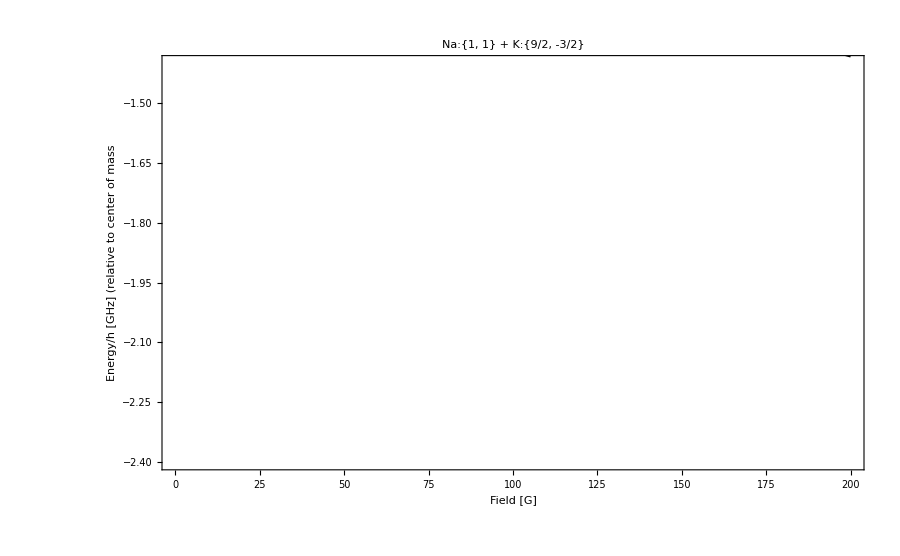

```mathematica
toPlot={4};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.4,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->900,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

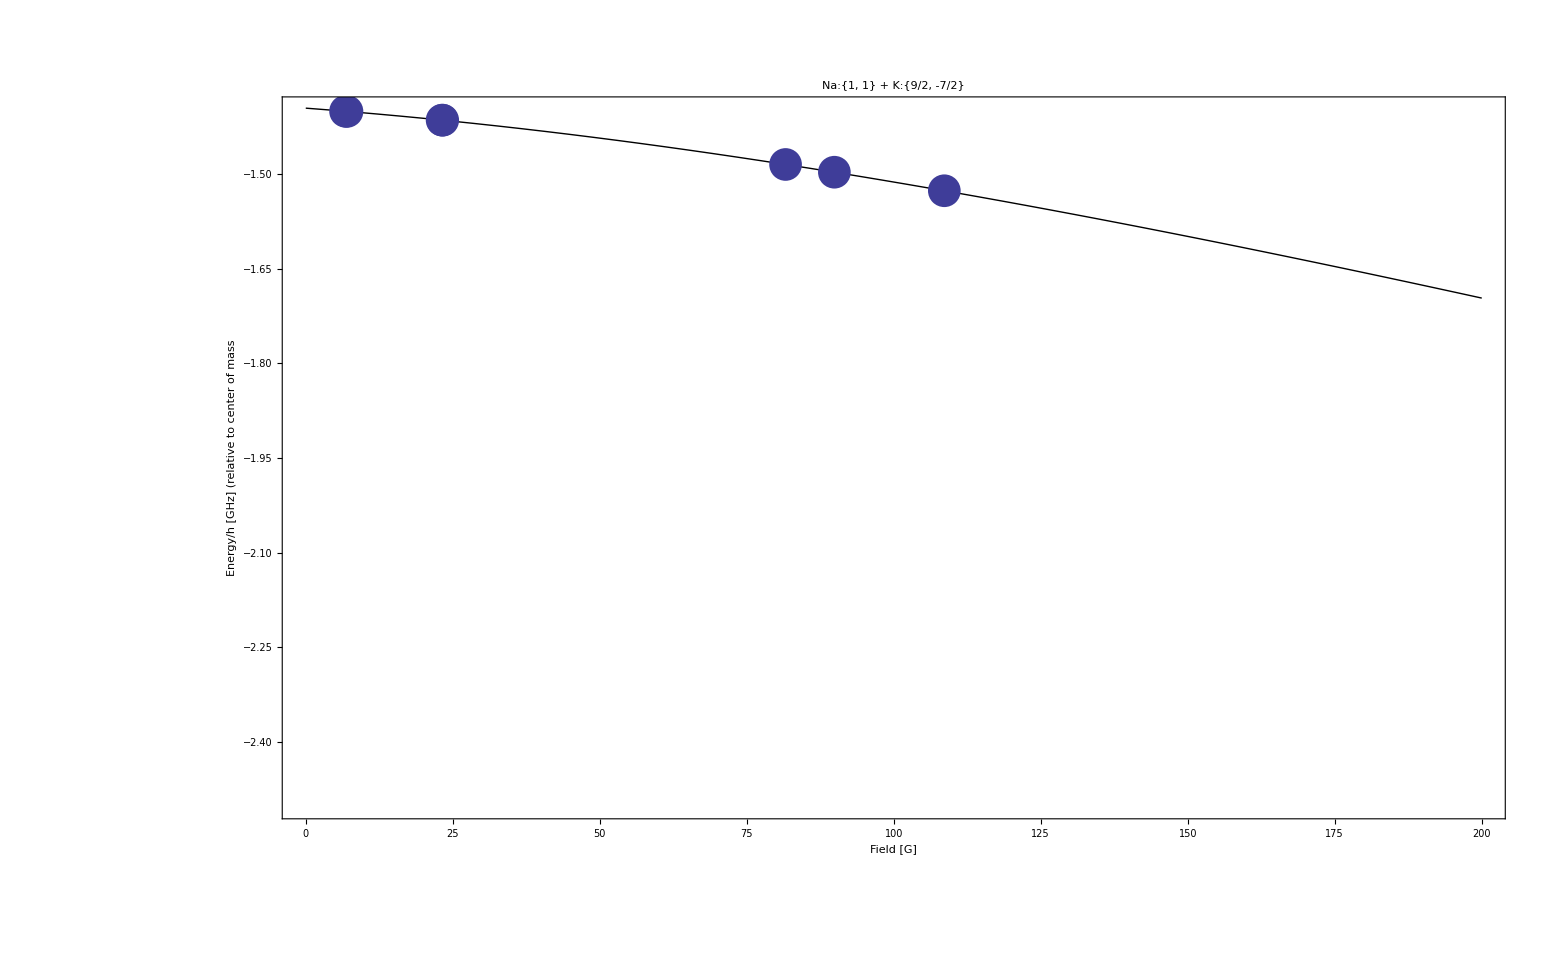

```mathematica
toPlot={2};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->1600,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

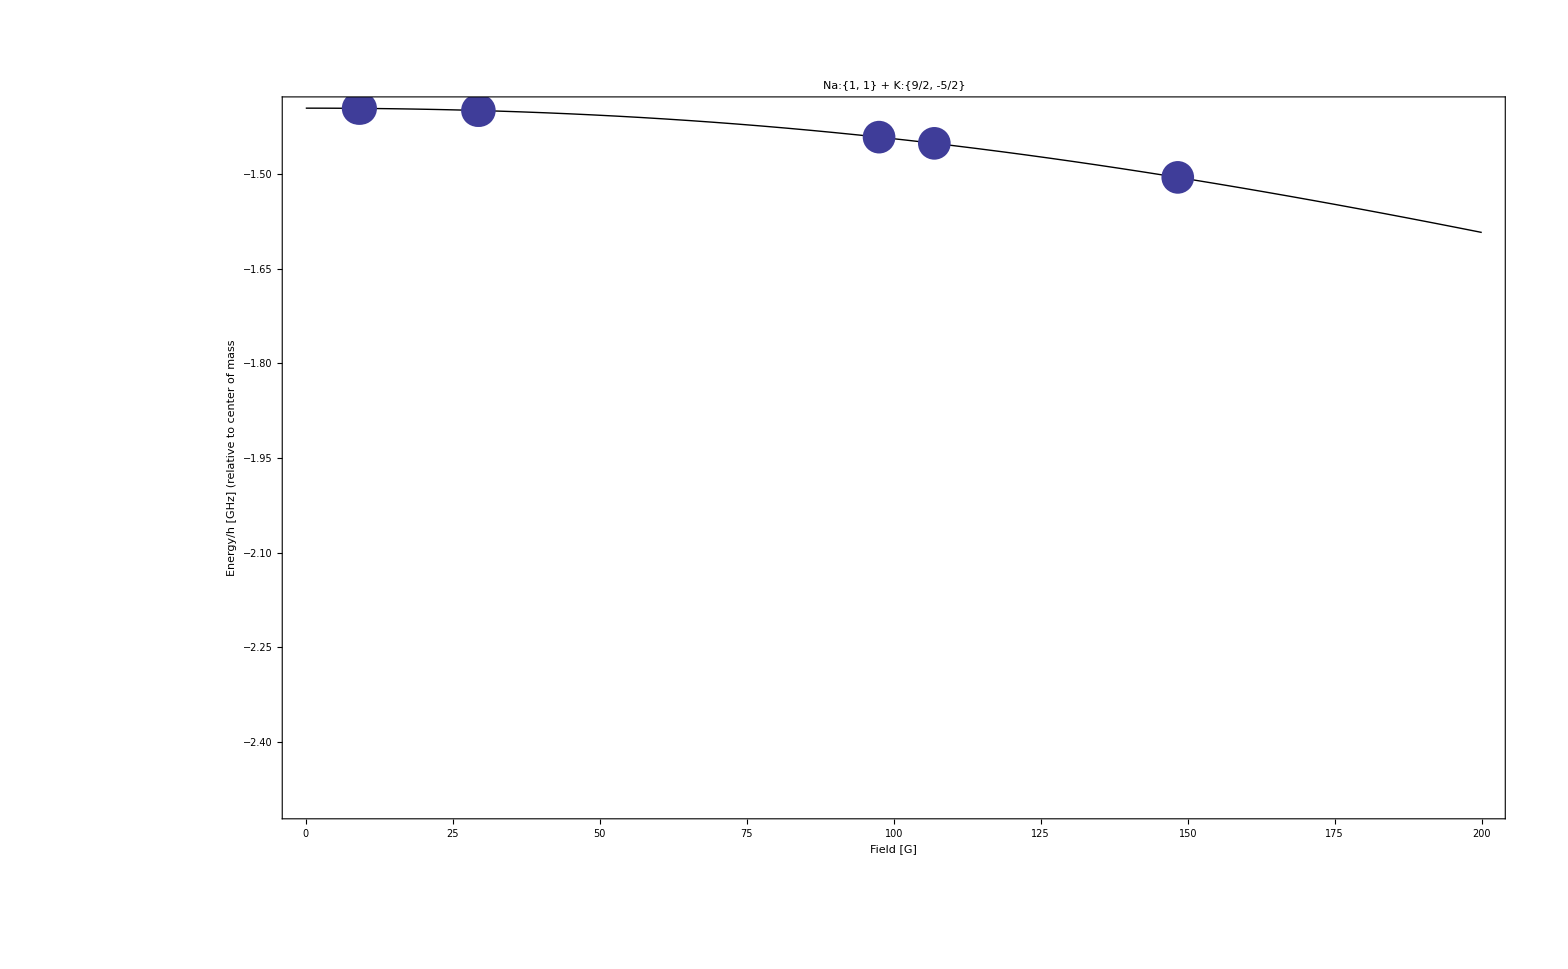

```mathematica
toPlot={3};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->1600,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

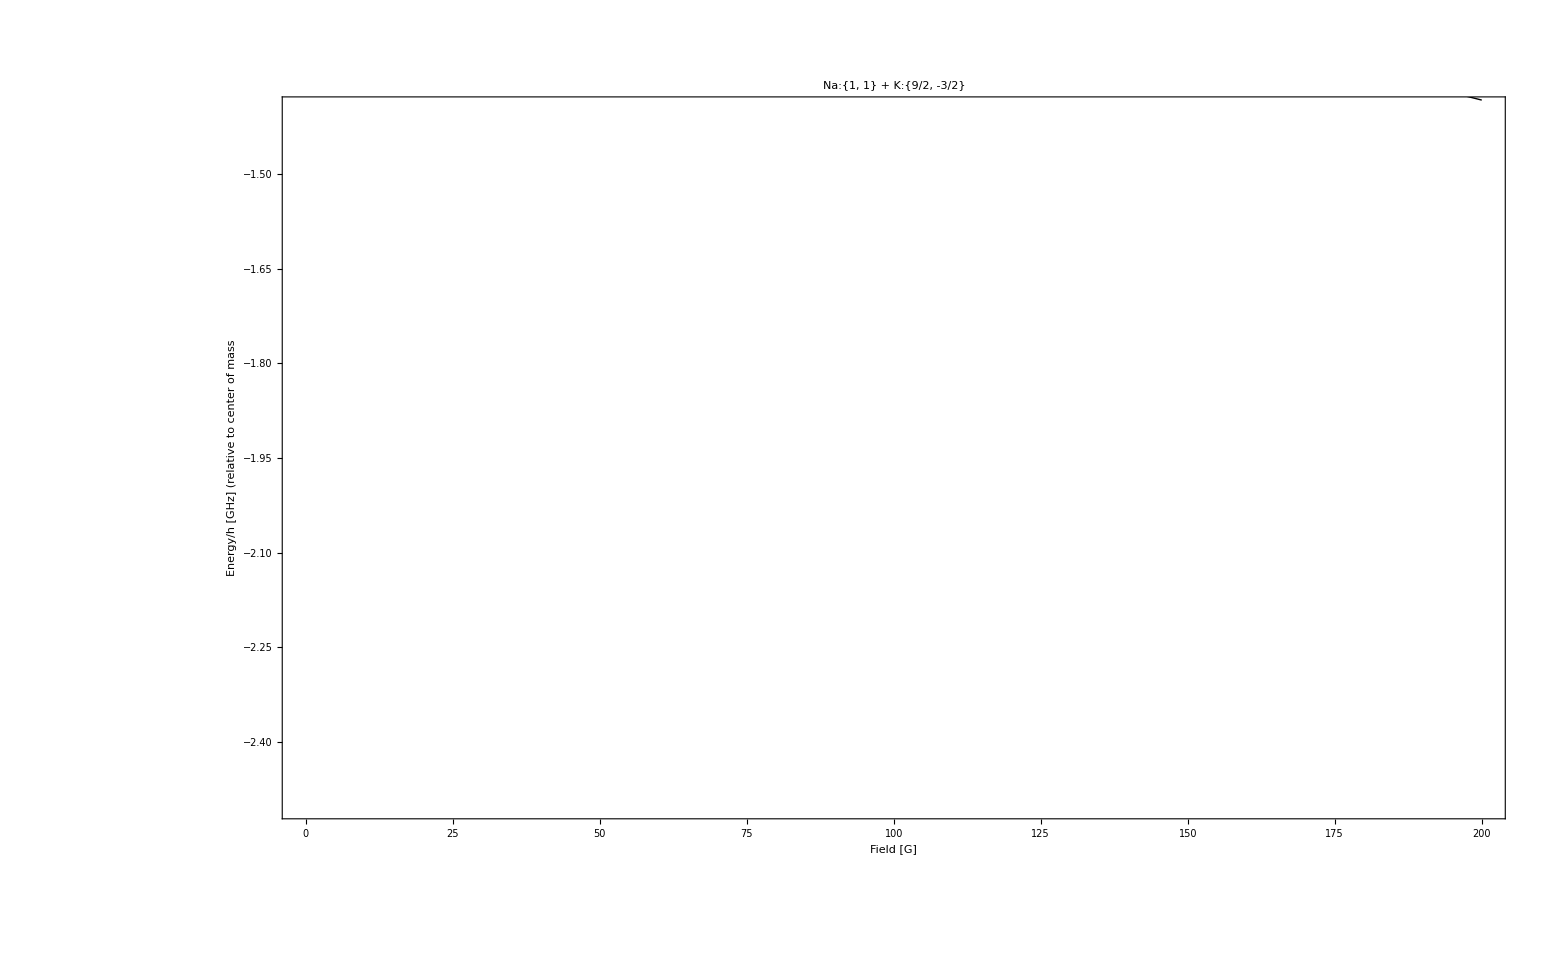

```mathematica
toPlot={4};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->1600,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification {} ⟦ 1 ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

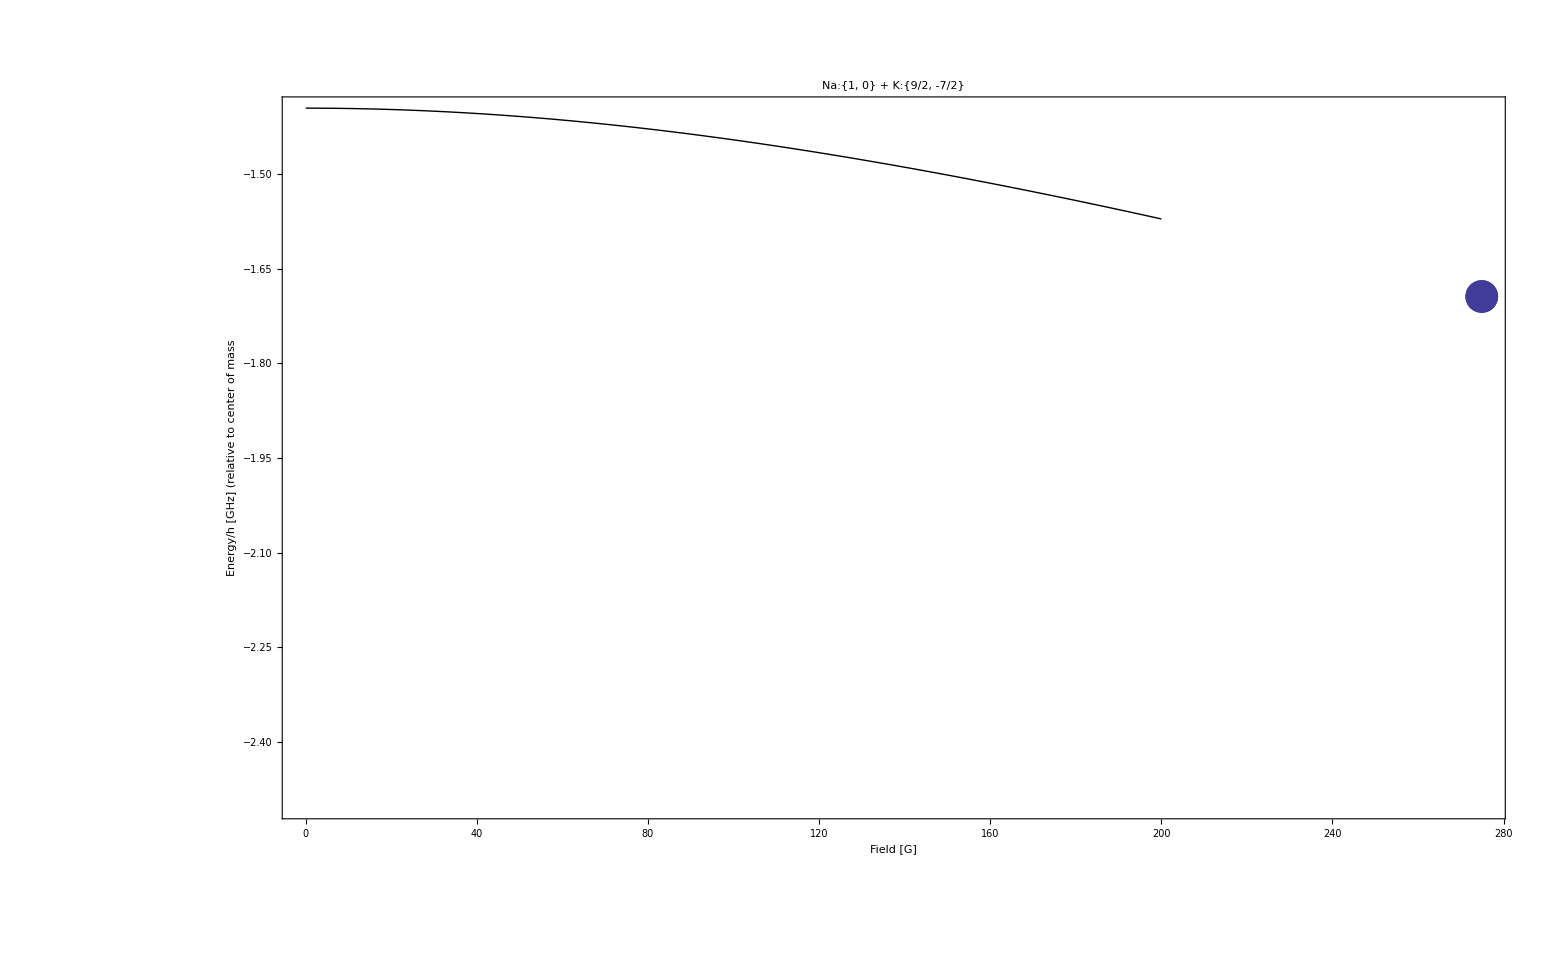

```mathematica
toPlot={10};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->1600,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```